## LU Decomposition

```mathematica
LU[A_]:=
(U=A;
n=Length[A];
L=Table[0,{n},{n}];
For[i=1,i≤n,i++,
L[[i,i]]=1
];
For[i=1, i≤n, i++,
For[j=i+1,j≤n,j++,
l=U[[j,i]]/U[[i,i]];
L[[j,i]]=l;
U[[j,i]]=0;
For[k=i+1,k≤n,k++,
U[[j,k]]=U[[j,k]]-l*U[[i,k]];
]
]
];
{L,U}
)
```

## LUSolve

```mathematica
LUSolve[L_,U_,b_]:=(
n=Length[b];
y=Table[0,{i,n}] ;
For[i=1,i≤n, i++,
y[[i]]=(b[[i]]-Sum[L[[i,j]]y[[j]],{j,1,i-1}])/L[[i,i]]

];
x=Table[0,{i,n}] ;
For[i=n,i≥1, i--,
x[[i]]=(y[[i]]-Sum[U[[i,j]]x[[j]],{j,i+1,n}])/U[[i,i]]

];
x
)
```

```mathematica
A={{6,0,-1,0,0},{-3,3,0,0,0},{0,-1,9,0,0},{0,-1,-8,11,-2},{-3,-1,0,0,4}}//N;
```

```mathematica
{LA,UA}=LU[A];
concentrations={10,30,50,70,80,90,100};
For[input1=1,input1≤Length[concentrations],input1++,
For[input2=1,input2≤Length[concentrations],input2++,
result=LUSolve[LA,UA,{5 concentrations[[input1]],0,8 concentrations[[input2]],0,0}];
Print["Input1: ",concentrations[[input1]]," Input2: ",concentrations[[input2]]," The result is: ",result];
];
];
```

Input1: 10 Input2: 10 The result is: {10.,10.,10.,10.,10.}

Input1: 10 Input2: 30 The result is: {13.0189,13.0189,28.1132,23.9966,13.0189}

Input1: 10 Input2: 50 The result is: {16.0377,16.0377,46.2264,37.9931,16.0377}

Input1: 10 Input2: 70 The result is: {19.0566,19.0566,64.3396,51.9897,19.0566}

Input1: 10 Input2: 80 The result is: {20.566,20.566,73.3962,58.988,20.566}

Input1: 10 Input2: 90 The result is: {22.0755,22.0755,82.4528,65.9863,22.0755}

Input1: 10 Input2: 100 The result is: {23.5849,23.5849,91.5094,72.9846,23.5849}

Input1: 30 Input2: 10 The result is: {26.9811,26.9811,11.8868,16.0034,26.9811}

Input1: 30 Input2: 30 The result is: {30.,30.,30.,30.,30.}

Input1: 30 Input2: 50 The result is: {33.0189,33.0189,48.1132,43.9966,33.0189}

Input1: 30 Input2: 70 The result is: {36.0377,36.0377,66.2264,57.9931,36.0377}

Input1: 30 Input2: 80 The result is: {37.5472,37.5472,75.283,64.9914,37.5472}

Input1: 30 Input2: 90 The result is: {39.0566,39.0566,84.3396,71.9897,39.0566}

Input1: 30 Input2: 100 The result is: {40.566,40.566,93.3962,78.988,40.566}

Input1: 50 Input2: 10 The result is: {43.9623,43.9623,13.7736,22.0069,43.9623}

Input1: 50 Input2: 30 The result is: {46.9811,46.9811,31.8868,36.0034,46.9811}

Input1: 50 Input2: 50 The result is: {50.,50.,50.,50.,50.}

Input1: 50 Input2: 70 The result is: {53.0189,53.0189,68.1132,63.9966,53.0189}

Input1: 50 Input2: 80 The result is: {54.5283,54.5283,77.1698,70.9949,54.5283}

Input1: 50 Input2: 90 The result is: {56.0377,56.0377,86.2264,77.9931,56.0377}

Input1: 50 Input2: 100 The result is: {57.5472,57.5472,95.283,84.9914,57.5472}

Input1: 70 Input2: 10 The result is: {60.9434,60.9434,15.6604,28.0103,60.9434}

Input1: 70 Input2: 30 The result is: {63.9623,63.9623,33.7736,42.0069,63.9623}

Input1: 70 Input2: 50 The result is: {66.9811,66.9811,51.8868,56.0034,66.9811}

Input1: 70 Input2: 70 The result is: {70.,70.,70.,70.,70.}

Input1: 70 Input2: 80 The result is: {71.5094,71.5094,79.0566,76.9983,71.5094}

Input1: 70 Input2: 90 The result is: {73.0189,73.0189,88.1132,83.9966,73.0189}

Input1: 70 Input2: 100 The result is: {74.5283,74.5283,97.1698,90.9949,74.5283}

Input1: 80 Input2: 10 The result is: {69.434,69.434,16.6038,31.012,69.434}

Input1: 80 Input2: 30 The result is: {72.4528,72.4528,34.717,45.0086,72.4528}

Input1: 80 Input2: 50 The result is: {75.4717,75.4717,52.8302,59.0051,75.4717}

Input1: 80 Input2: 70 The result is: {78.4906,78.4906,70.9434,73.0017,78.4906}

Input1: 80 Input2: 80 The result is: {80.,80.,80.,80.,80.}

Input1: 80 Input2: 90 The result is: {81.5094,81.5094,89.0566,86.9983,81.5094}

Input1: 80 Input2: 100 The result is: {83.0189,83.0189,98.1132,93.9966,83.0189}

Input1: 90 Input2: 10 The result is: {77.9245,77.9245,17.5472,34.0137,77.9245}

Input1: 90 Input2: 30 The result is: {80.9434,80.9434,35.6604,48.0103,80.9434}

Input1: 90 Input2: 50 The result is: {83.9623,83.9623,53.7736,62.0069,83.9623}

Input1: 90 Input2: 70 The result is: {86.9811,86.9811,71.8868,76.0034,86.9811}

Input1: 90 Input2: 80 The result is: {88.4906,88.4906,80.9434,83.0017,88.4906}

Input1: 90 Input2: 90 The result is: {90.,90.,90.,90.,90.}

Input1: 90 Input2: 100 The result is: {91.5094,91.5094,99.0566,96.9983,91.5094}

Input1: 100 Input2: 10 The result is: {86.4151,86.4151,18.4906,37.0154,86.4151}

Input1: 100 Input2: 30 The result is: {89.434,89.434,36.6038,51.012,89.434}

Input1: 100 Input2: 50 The result is: {92.4528,92.4528,54.717,65.0086,92.4528}

Input1: 100 Input2: 70 The result is: {95.4717,95.4717,72.8302,79.0051,95.4717}

Input1: 100 Input2: 80 The result is: {96.9811,96.9811,81.8868,86.0034,96.9811}

Input1: 100 Input2: 90 The result is: {98.4906,98.4906,90.9434,93.0017,98.4906}

Input1: 100 Input2: 100 The result is: {100.,100.,100.,100.,100.}

```mathematica
AInverse[A_]:=(
{L,U}=LU[A];
n=Length[A];
inverseMatrix=Table[0,{n},{n}];
For[k=1,k≤n,k++,
b=Table[If[1==k,1,0],{l,1,n}];
inverseMatrix[[All,k]]=LUSolve[L,U,b];
];
inverseMatrix
)
```

```mathematica
AInverse[{{1,2,3},{4,2,2},{5,1,7}}]
```

{{1/42,0,0},{8/21,0,0},{1/14,0,0}}

```mathematica
Sqrt[73]//N
```

8.544

```mathematica
Clear[f,x,y]
```

```mathematica
f[x_,y_]=3 x^2+8 x y+6 y^2;
Plot3D[f[x,y],{x,-50,50},{y,-50,50}]
```

-Graphics3D-

```mathematica
-m-6-((1*(-2*m-4)))/2
```

-6-m+1/2 (4+2 m)

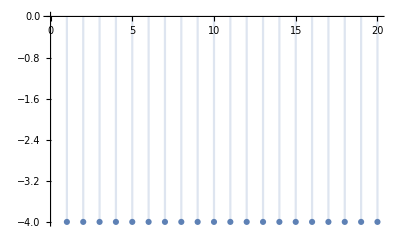

```mathematica
DiscretePlot[-6-m+1/2 (4+2 m),{m,1,20}]
```

```mathematica
Simplify[-6-m+1/2 (4+2 m)]
```

-4